```mathematica
whitetoblacksort[dimer_]:=If[EvenQ[Total[dimer⟦1⟧]],dimer,Reverse[dimer]]
```

```mathematica
(*graphics for dominoes*)
domino2D[{{a_,b_},{c_,d_}}]:=Rectangle[{Min[a,c]-1/2,Min[b,d]-1/2},{Max[a,c]+1/2,Max[b,d]+1/2}]
domino3D [{{a_,b_,c_},{d_,e_,f_}}]:=Cuboid[{Min[a,d]-1/2,Min[b,e]-1/2,Min[c,f]-1/2},{Max[a,d]+1/2,Max[b,e]+1/2,Max[c,f]+1/2}]
(*for making slices in 3D (clip cuts off the 3rd coordinate of the domino)*)
clip3[{{a_,b_,c_},{d_,e_,f_}}]:={{a,b},{d,e}}
clip1[{{a_,b_,c_},{d_,e_,f_}}]:={{b,c},{e,f}}
clip2[{{a_,b_,c_},{d_,e_,f_}}]:={{a,c},{d,f}}
(*color functions*)
brickColor=Hue[0.03,1,0.8];
fourcolor2D[{{a_,b_},{c_,d_}}]:=Which[a-c==0&&OddQ[Floor[Min[b,d]-Floor[a]]],Hue[5/6,1,1/2],a-c==0&&EvenQ[Floor[Min[b,d]-Floor[a]]],Hue[0.08,0.87,0.94],Abs[a-c]==1&&OddQ[Floor[Min[a,c]]-Floor[b]],Hue[0.56,0.65,0.93],Abs[a-c]==1&&EvenQ[Floor[Min[a,c]]-Floor[b]],Hue[0.29,0.88,0.87]]
sixcolor3D[{{a_,b_,c_},{d_,e_,f_}}]:=Which[a-d==0&&c-f==0&&Abs[b-e]==1&&OddQ[Floor[Min[b,e]]+Floor[a]+Floor[c]],Hue[5/6,1,1/2],a-d==0&&c-f==0&&Abs[b-e]==1&&EvenQ[Floor[Min[b,e]]+Floor[a]+Floor[c]],Hue[0.08,0.87,0.94],Abs[a-d]==1&&b-e==0&&c-f==0&&OddQ[Floor[Min[a,d]]+Floor[b]+Floor[c]],Hue[0.56,0.65,0.93],Abs[a-d]==1&&b-e==0&&c-f==0&&EvenQ[Floor[Min[a,d]]+Floor[b]+Floor[c]],Hue[0.29,0.88,0.87],a-d==0&&b-e==0&&Abs[c-f]==1&&OddQ[Floor[Min[c,f]]+Floor[a]+Floor[b]], Hue[0,0.97,0.94],a-d==0&&b-e==0&&Abs[c-f]==1&&EvenQ[Floor[Min[c,f]]+Floor[a]+Floor[b]],Hue[0.15,1,1]]
```

```mathematica
my3Dcolors={Hue[0.15, 1, 1],Hue[0, 0.97, 0.94],Hue[0.08, 0.87, 0.94],Hue[Rational[5, 6], 1, Rational[1, 2]],Hue[0.29, 0.88, 0.87],Hue[0.56, 0.65, 0.93]};
my2Dcolors={Hue[0.08, 0.87, 0.94],Hue[Rational[5, 6], 1, Rational[1, 2]],Hue[0.29, 0.88, 0.87],Hue[0.56, 0.65, 0.93]};
```

```mathematica
(*2D*)
grid2D[n_,m_]:=grid2D[n,m]=Flatten[Table[{a,b},{a,0,n-1},{b,0,m-1}],1]
sbricks2D[n_,m_]:=sbricks2D[n,m]=whitetoblacksort[#]&/@Partition[grid2D[n,m],2]
(*3D*)
grid3D[n_,m_,k_]:=grid3D[n,m,k]=Flatten[Table[{a,b,c},{a,0,n-1},{b,0,m-1},{c,0,k-1}],2];
sbricks3D[n_,m_,k_]:=sbricks3D[n,m,k]=whitetoblacksort[#]&/@Partition[grid3D[n,m,k],2]
```

```mathematica
(*variants of the aztec diamond*)
coordinator[{x_,list_}]:=Table[{x,list[[i]]},{i,1,Length[list]}]
(*2D aztec diamond*)
aztecgrid[k_]:=aztecgrid[k]=Catenate[Map[coordinator,Partition[Riffle[Table[i+1/2,{i,-k,k}],Join[Reverse[Table[Table[i-1/2,{i,-n+1,n}],{n,k,1,-1}]],Table[Table[i-1/2,{i,-n+1,n}],{n,k,1,-1}]]],2]]]
aztecbricks[k_]:=aztecbricks[k]=Partition[aztecgrid[k],2]
saztecbricks[k_]:=whitetoblacksort[#]&/@aztecbricks[k]
(*aztec octahedron*)
aztechedron[k_]:=aztechedron[k]=Catenate[Join[Table[Append[#,k-m+1/2]&/@aztecgrid[Abs[m]],{m,0,k}],Table[Append[#,m-k-1+1/2]&/@aztecgrid[Abs[m]],{m,0,k}]]]
aztechedronbricks[k_]:=aztechedronbricks[k]=Partition[aztechedron[k],2]
saztechedron[k_]:=aztechedron[k]+1/2
saztechedronbricks[k_]:=saztechedronbricks[k]=whitetoblacksort[#]&/@Evaluate[aztechedronbricks[k]+1/2]
(*aztec prism*)
aztecprism[k_,n_]:=aztecprism[k,n]=Flatten[#,1]&/@SortBy[Catenate[Table[{aztecgrid[k][[i]],j},{i,1,Length[aztecgrid[k]]},{j,1,n}]],Last]
aztecprismbricks[k_,n_]:=aztecprismbricks[k,n]=Partition[aztecprism[k,n],2]
saztecprismbricks[k_,n_]:=saztecprismbricks[k,n]=whitetoblacksort[#]&/@aztecprismbricks[k,n]
```

```mathematica
neighbors[point_,grid_]:=Complement[Nearest[grid,point,{7,1}],{point}]
```

```mathematica
dominoes[point_,grid_]:={point,#}&/@neighbors[point,grid]
```

```mathematica
randomdirectionbrick[brick_,grid_]:=RandomChoice[DeleteCases[dominoes[Last[brick],grid],Reverse[brick]]]
```

```mathematica
nextbrick[brick_,tiling_]:=Catenate[Select[tiling,MemberQ[#,Last[brick]]&]]
```

```mathematica
loopshift[dimerloop_]:=Reverse[#]&/@Partition[RotateLeft[Catenate[dimerloop]],2]
```

```mathematica
openloop[path_]:=If[Max[Counts[Catenate[path]]]<3&&Count[Catenate[path],First[Catenate[path]]]<2,True,False]
```

```mathematica
droptail[loop_]:=Partition[Take[Catenate[loop],Flatten[Take[Position[Catenate[loop],Last[Catenate[loop]]],-2]]],2]
```

```mathematica
randomloop[grid_,tiling_]:=droptail[Module[{brick,preloop,time,closetime,tailoop},brick[1]=RandomChoice[tiling];
brick[2]=randomdirectionbrick[brick[1],grid];
brick[3]=nextbrick[brick[2],tiling];
brick[k_]:=brick[k]=If[EvenQ[k],randomdirectionbrick[brick[k-1],grid],nextbrick[brick[k-1],tiling]];
preloop[n_]:=preloop[n]=Table[brick[j],{j,1,n}];
For[n=1,n<Length[grid],n++,If[openloop[preloop[n]]==False,Break[]]];closetime=n;
tailoop=preloop[closetime];
tailoop]]
```

```mathematica
randomloopshift[{grid_,tiling_}]:=Module[{doubleloop,oldloop,newloop,newtiles},doubleloop=randomloop[grid,tiling];
oldloop=doubleloop[[1;;-1;;2]];
newloop=loopshift[oldloop];newtiles=Union[newloop,Complement[tiling,oldloop]];
{grid,newtiles}]
```

```mathematica
loopshiftrandomtiling2D[grid_,tiling_,N_]:=Timing[Graphics[{EdgeForm[{Thin,White}],fourcolor2D[#],domino2D[#]}&/@Last[Nest[randomloopshift,{grid,tiling},N]]]]
```

```mathematica
loopshiftrandomtiling3D[grid_,tiling_,N_]:=Timing[Graphics3D[{EdgeForm[{Thin,White}],sixcolor3D[#],domino3D[#]}&/@Last[Nest[randomloopshift,{grid,tiling},N]]]]
```

```mathematica
loopshiftrandomtiling3Dslices[grid_,tiling_,N_,min_,max_,spacing_]:=Timing[Block[{randomtiling},
randomtiling=Last[Nest[randomloopshift,{grid,tiling},N]];{Graphics3D[{EdgeForm[{White,Thin}],sixcolor3D[#],domino3D[#]}&/@randomtiling],
Table[Graphics[{EdgeForm[{White,Thin}],sixcolor3D[#],domino2D[clip3[#]]}&/@Select[randomtiling,Or[#[[2]][[3]]==i,#[[1]][[3]]==i]&]],{i,min,max,spacing}]}]]
```

```mathematica
loopshiftrandomtiling3Dallslices[grid_,tiling_,N_,min_,max_,spacing_]:=AbsoluteTiming[Block[{randomtiling},
randomtiling=Last[Nest[randomloopshift,{grid,tiling},N]];{randomtiling,Graphics3D[{EdgeForm[{White,Thin}],sixcolor3D[#],domino3D[#]}&/@randomtiling,Boxed->False],
Table[Graphics[{EdgeForm[{White,Thin}],sixcolor3D[#],domino2D[clip3[#]]}&/@Select[randomtiling,Or[#[[2]][[3]]==i,#[[1]][[3]]==i]&]],{i,min,max,spacing}],Table[Graphics[{EdgeForm[{White,Thin}],sixcolor3D[#],domino2D[clip2[#]]}&/@Select[randomtiling,Or[#[[2]][[2]]==i,#[[1]][[2]]==i]&]],{i,min,max,spacing}],Table[Graphics[{EdgeForm[{White,Thin}],sixcolor3D[#],domino2D[clip1[#]]}&/@Select[randomtiling,Or[#[[2]][[1]]==i,#[[1]][[1]]==i]&]],{i,min,max,spacing}]}]]
```

Use the last function, with the regions and bricks that start with “s” (for sorted). E.g.:

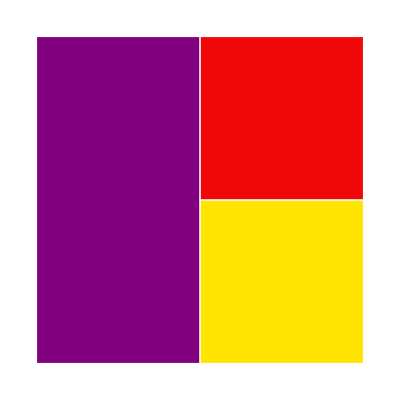
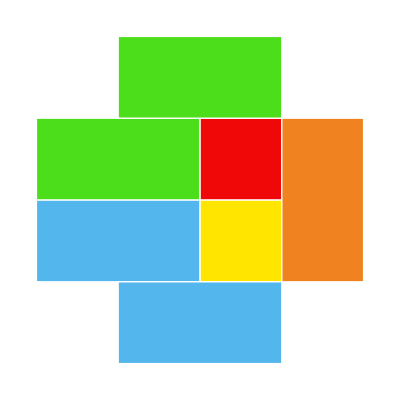
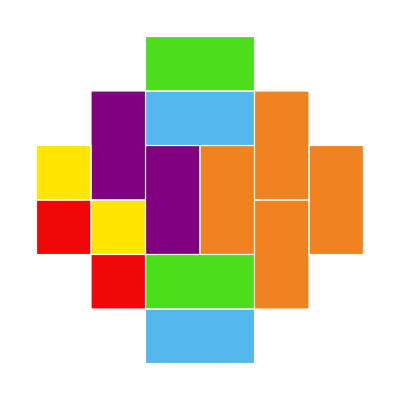
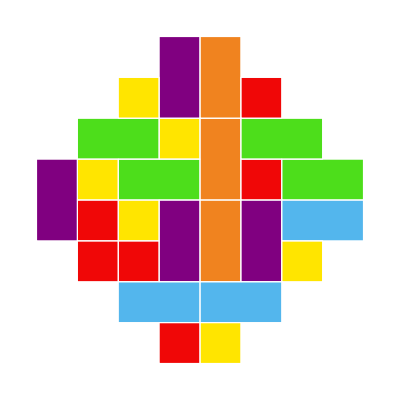
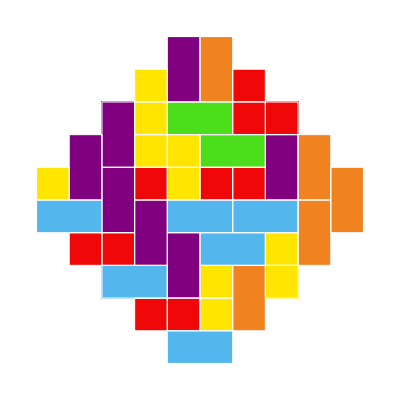
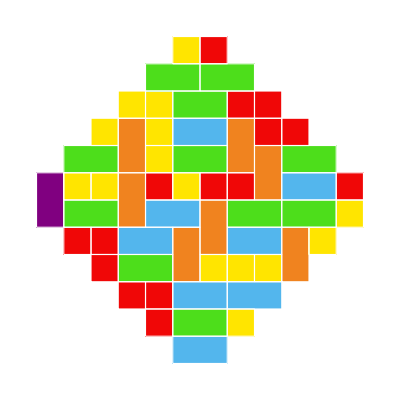
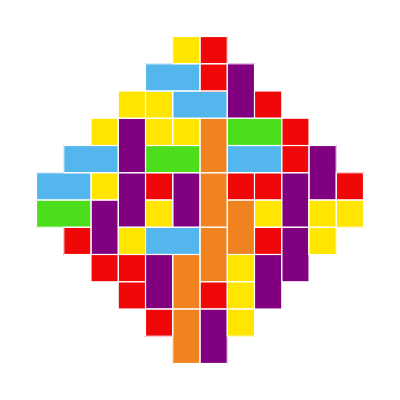
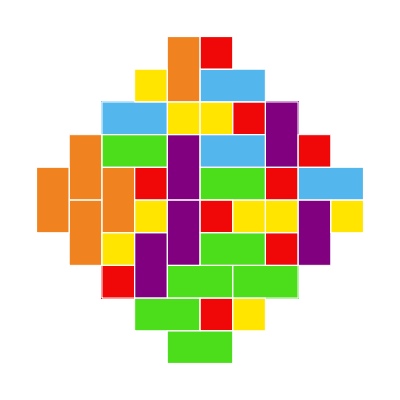
{62.2934,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[6],saztechedronbricks[6],5000,-5,6,1]
```

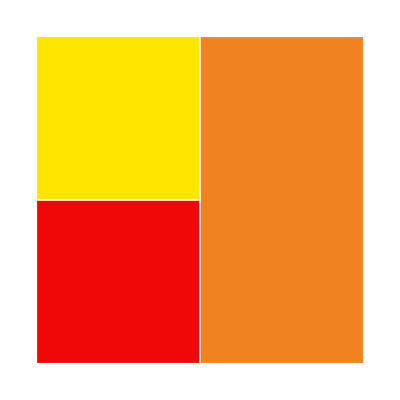
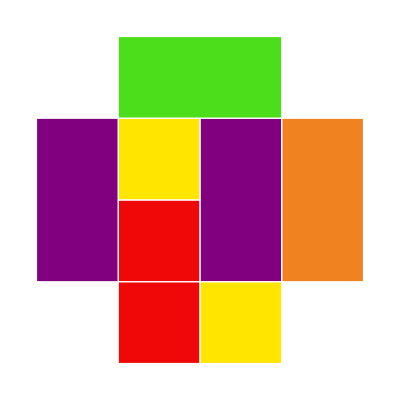
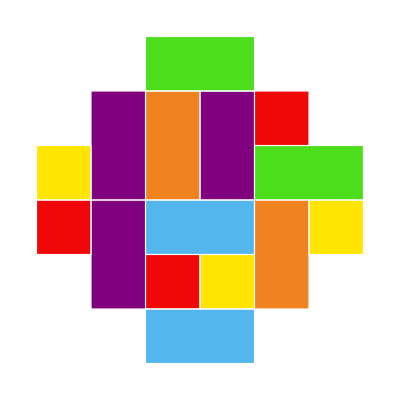
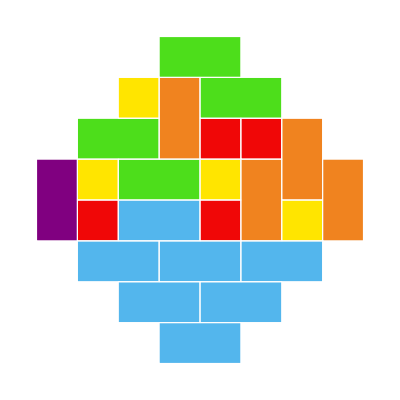
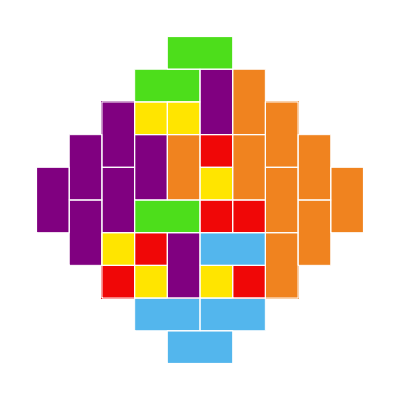
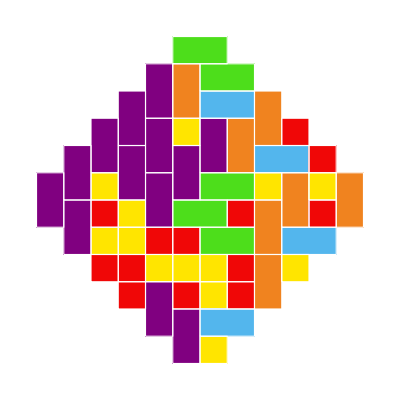
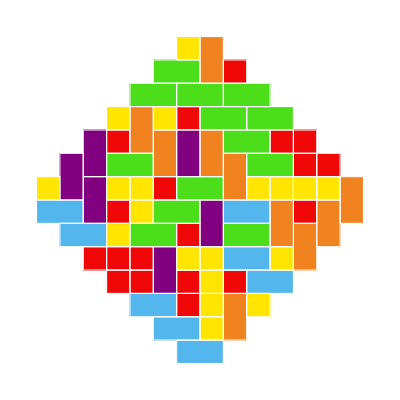
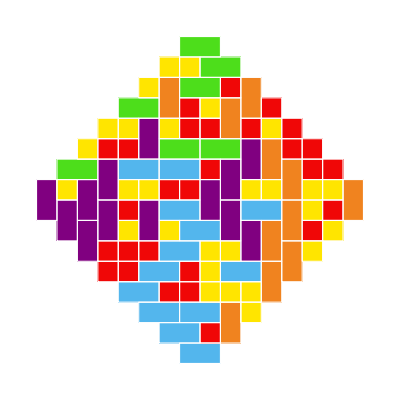
{219.201,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[10],saztechedronbricks[10],5000,-9,10,1]
```

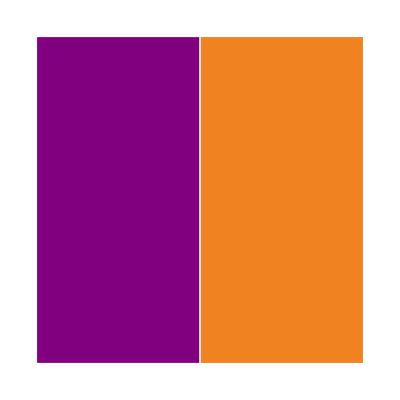
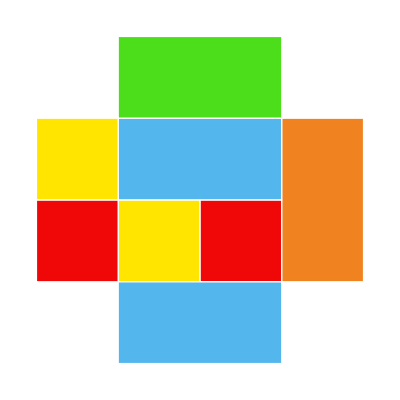
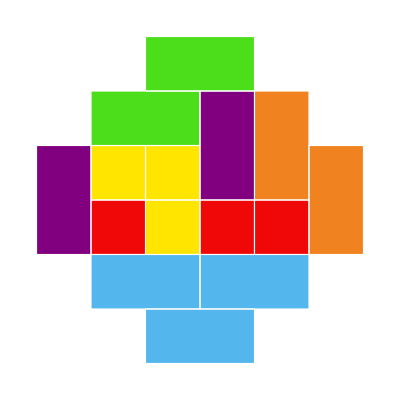
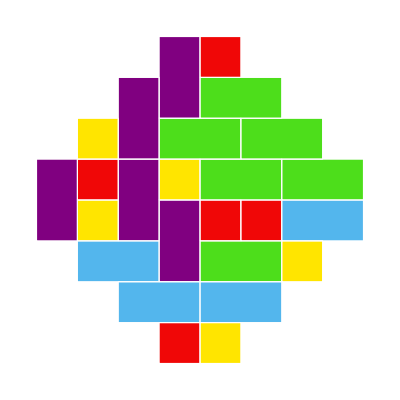
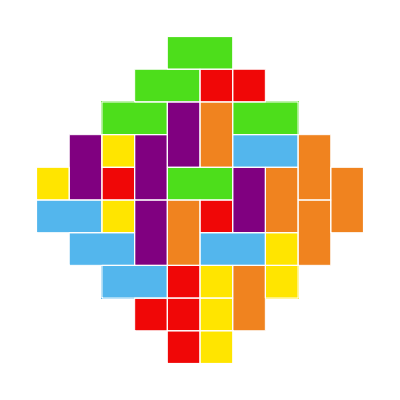
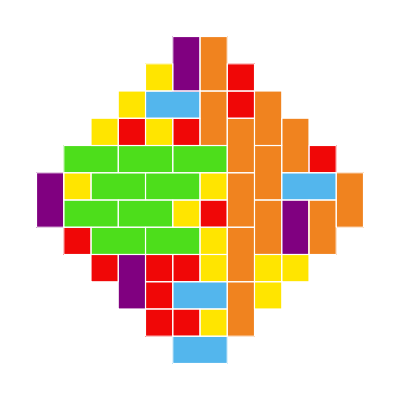
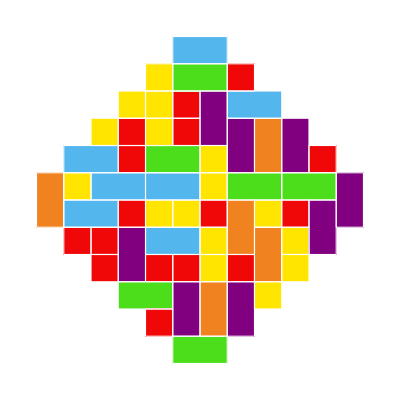
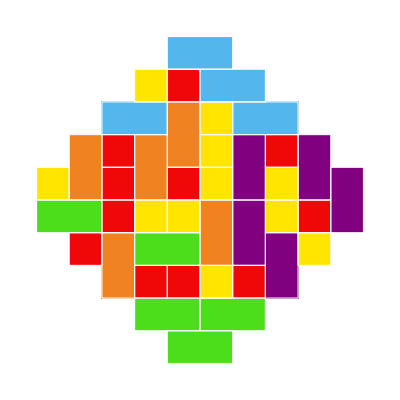
{1.78463,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dallslices[saztechedron[6],saztechedronbricks[6],100,-5,6,1]
```

```mathematica
aztecgrid[4]
```

{{-7/2,-1/2},{-7/2,1/2},{-5/2,-3/2},{-5/2,-1/2},{-5/2,1/2},{-5/2,3/2},{-3/2,-5/2},{-3/2,-3/2},{-3/2,-1/2},{-3/2,1/2},{-3/2,3/2},{-3/2,5/2},{-1/2,-7/2},{-1/2,-5/2},{-1/2,-3/2},{-1/2,-1/2},{-1/2,1/2},{-1/2,3/2},{-1/2,5/2},{-1/2,7/2},{1/2,-7/2},{1/2,-5/2},{1/2,-3/2},{1/2,-1/2},{1/2,1/2},{1/2,3/2},{1/2,5/2},{1/2,7/2},{3/2,-5/2},{3/2,-3/2},{3/2,-1/2},{3/2,1/2},{3/2,3/2},{3/2,5/2},{5/2,-3/2},{5/2,-1/2},{5/2,1/2},{5/2,3/2},{7/2,-1/2},{7/2,1/2}}

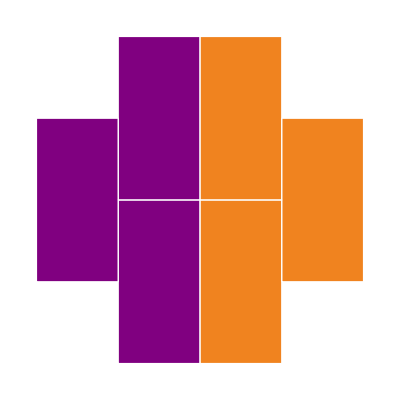
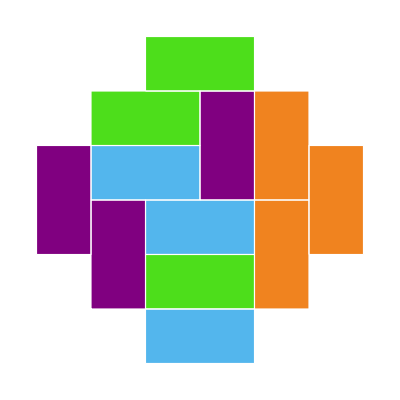
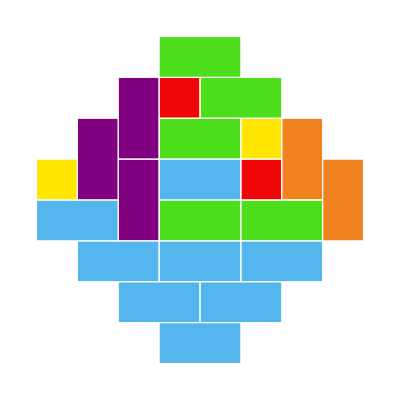
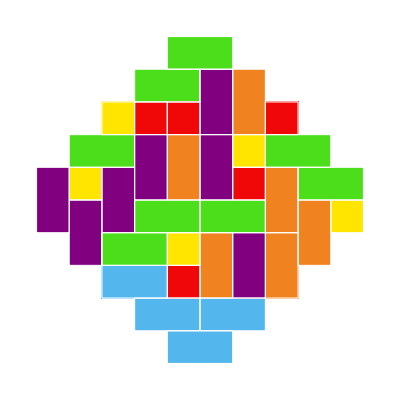
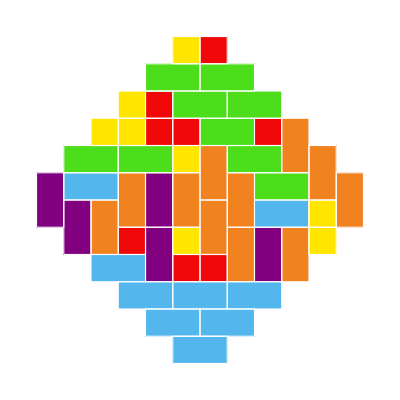
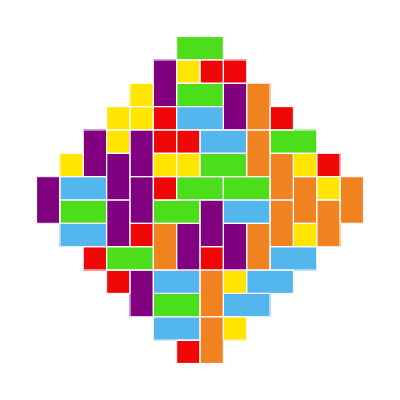
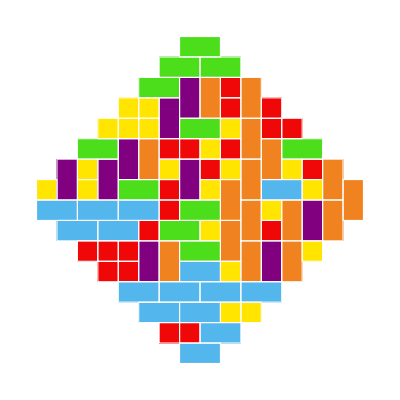
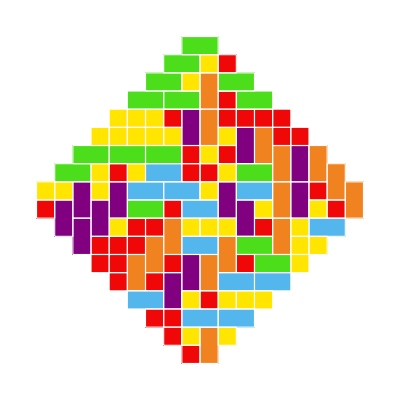
{458.46,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[10],saztechedronbricks[10],10000,-9,10,1]
```

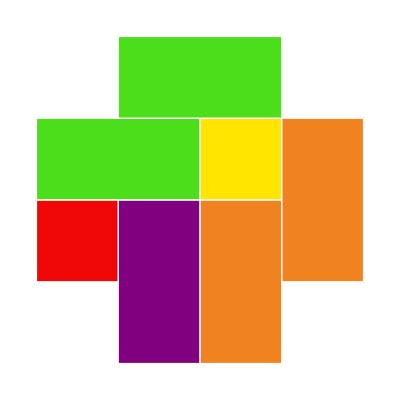
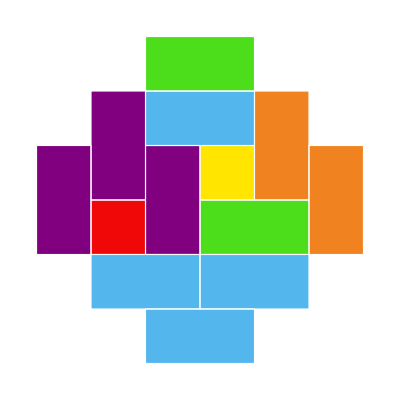
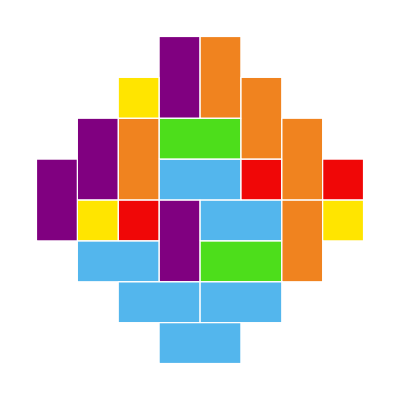
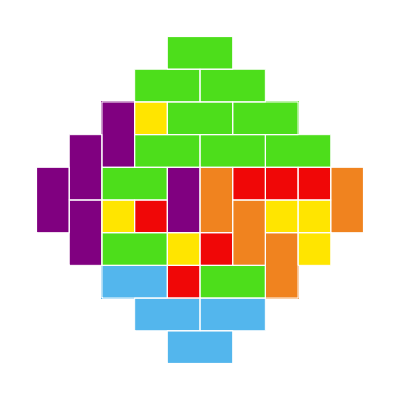
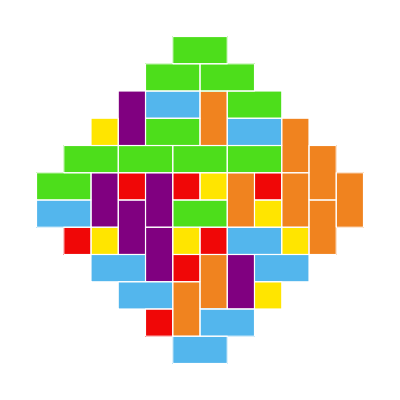
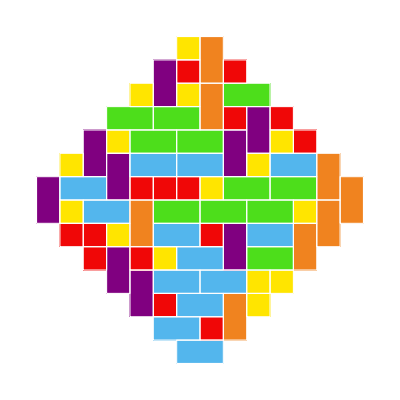
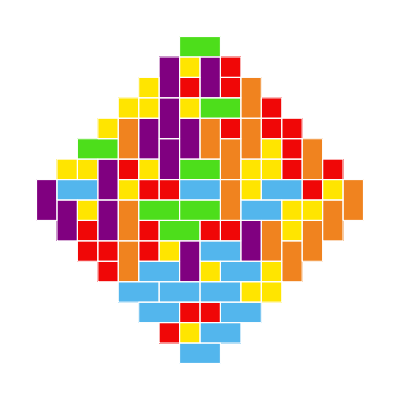
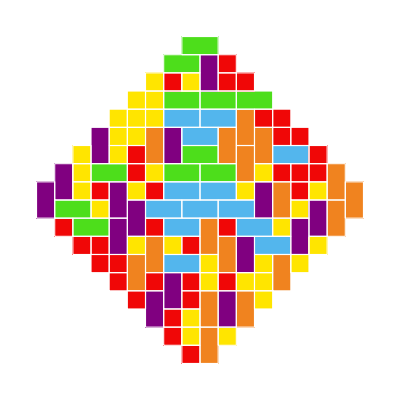
{1106.77,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[10],saztechedronbricks[10],25000,-9,10,1]
```

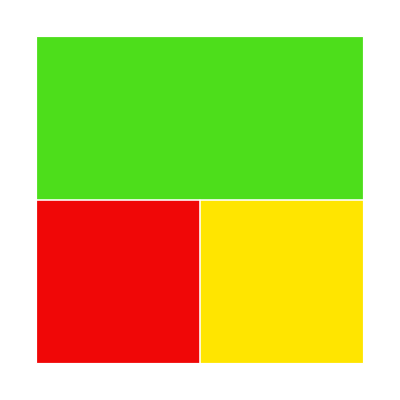
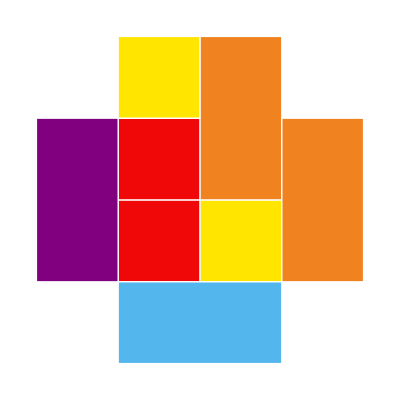
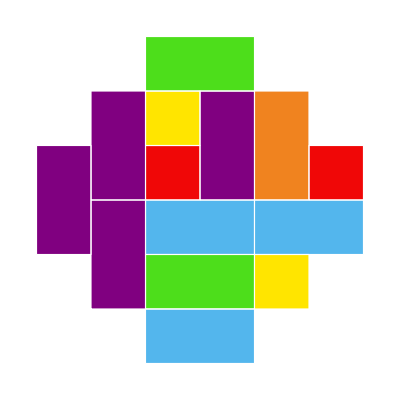
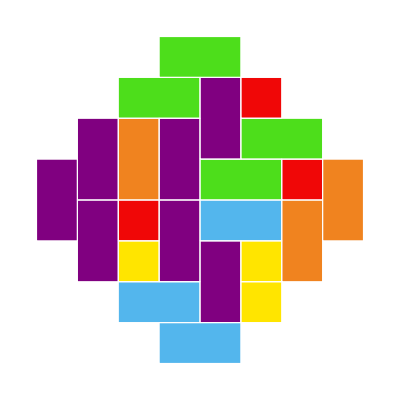
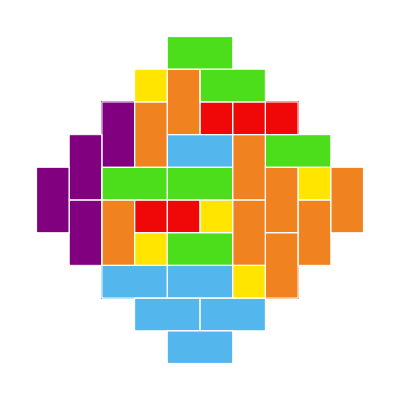
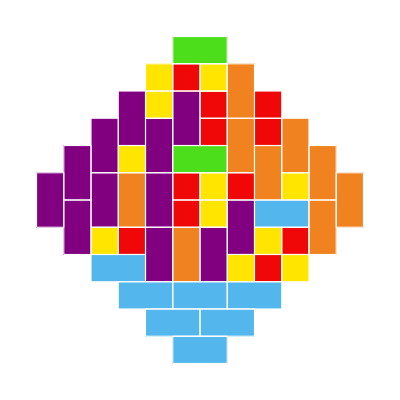
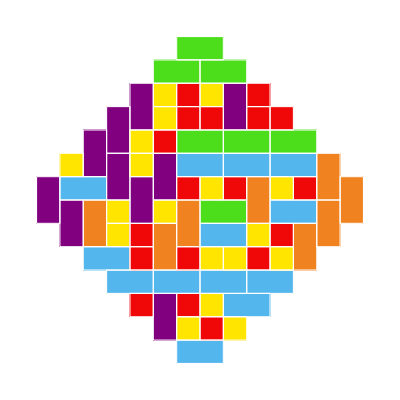
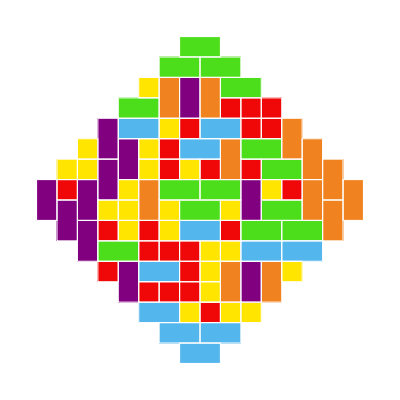
{1934.64,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[10],saztechedronbricks[10],40000,-9,10,1]
```

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[15],saztechedronbricks[15],40000,-14,15,1]
```

{5915.95,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[aztecprism[10,3],saztecprismbricks[10,3],10000,0,3,1]
```

{219.195,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[aztecprism[10,2],saztecprismbricks[10,2],10000,1,2,1]
```

{107.453,{-Graphics3D-,{-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[aztecprism[10,2],saztecprismbricks[10,2],20000,1,2,1]
```

{204.747,{-Graphics3D-,{-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[aztecprism[10,2],saztecprismbricks[10,2],50000,1,2,1]
```

{510.867,{-Graphics3D-,{-Graphics-,-Graphics-}}}

```mathematica
loopshiftrandomtiling3Dslices[saztechedron[15],saztechedronbricks[15],100000,-14,15,1]
```

{14852.3,{-Graphics3D-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}